```mathematica
SetDirectory[NotebookDirectory[]];
```

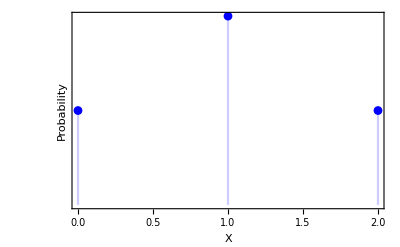

```mathematica
g=DiscretePlot[PDF[BinomialDistribution[2,0.5],x],{x,0,2},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,None}]
```

```mathematica
Export["binomial.pdf",g]
```

binomial.pdf

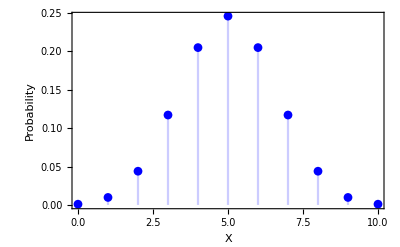

```mathematica
g=DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True}]
```

```mathematica
Export["binomial_10.pdf",g]
```

binomial_10.pdf

```mathematica
glist=Table[DiscretePlot[PDF[BinomialDistribution[10,θ],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True},PlotRange->{Automatic,{-0.04,1.01}},PlotLabel->StringJoin["Pr(H) = θ = ", ToString@NumberForm[θ,{3,2}]]],{θ,0,1,0.05}];
```

```mathematica
Table[Export[StringJoin["./animations/binomial_biased_",ToString@i,".pdf"],glist[[i]]],{i,1,Length@glist,1}]
```

{./animations/binomial_biased_1.pdf,./animations/binomial_biased_2.pdf,./animations/binomial_biased_3.pdf,./animations/binomial_biased_4.pdf,./animations/binomial_biased_5.pdf,./animations/binomial_biased_6.pdf,./animations/binomial_biased_7.pdf,./animations/binomial_biased_8.pdf,./animations/binomial_biased_9.pdf,./animations/binomial_biased_10.pdf,./animations/binomial_biased_11.pdf,./animations/binomial_biased_12.pdf,./animations/binomial_biased_13.pdf,./animations/binomial_biased_14.pdf,./animations/binomial_biased_15.pdf,./animations/binomial_biased_16.pdf,./animations/binomial_biased_17.pdf,./animations/binomial_biased_18.pdf,./animations/binomial_biased_19.pdf,./animations/binomial_biased_20.pdf,./animations/binomial_biased_21.pdf}

## Cumulative distribution function

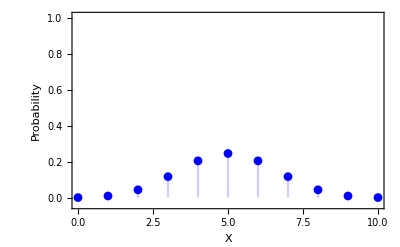

```mathematica
g1=Show[DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True},PlotRange->{Automatic,{-0.04,1.01}}]]
```

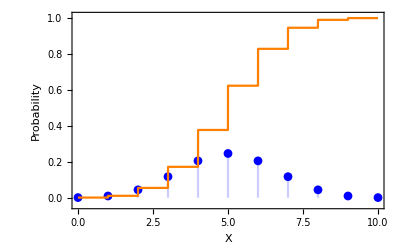

```mathematica
g2=Show[DiscretePlot[PDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Blue,Frame->{True,True,False,False},PlotMarkers->{Automatic, 9},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True},PlotRange->{Automatic,{-0.04,1.01}}],Plot[CDF[BinomialDistribution[10,0.5],x],{x,0,10},PlotStyle->Orange,Frame->{True,True,False,False},FrameLabel->{"X","Probability"},LabelStyle->{Black,FontSize->16},FrameTicks->{True,True},Exclusions->None]]
```

```mathematica
Export["binomial_cdf_1.pdf",g1]
Export["binomial_cdf_2.pdf",g2]
```

binomial_cdf_1.pdf

binomial_cdf_2.pdf